Active microswimmer in bulk fluid

```mathematica
ClearAll["Global`*"];
(*Unprotect[Cot,Csc,Sec];
Format[Cot[x_]]:=HoldForm[1/Tan[x]];
Format[Csc[x_]]:=HoldForm[1/Sin[x]];
Format[Sec[x_]]:=HoldForm[1/Cos[x]];
Protect[Cot,Csc,Sec];*)
<<"BVPh2_0.m"
```

Package BVPh.m was successfully loaded from C:\Program Files\Wolfram Research\Mathematica\11.3\AddOns\Applications\BVPh2_0.m !

Last updated by Yin-long Zhao, 00:22, Apr. 26, 2013.

```mathematica
(*wx=-1.31816782*^-03;
wy=-1.23482706*^-03;
wz=-7.57091305*^-01;*)
wz1=wz+1;
TypeEQ = 1;
TypeL = 2;
ApproxQ = 0;
HYBRID = 0; 
TypeBase = 1;
Ntruncated = 30;
FLOAT = 0;
c0[1] = -1;
c0[2] = -1;
(*th0 = Pi/2;*)
(*ps0=0;*)

NumEQ = 2;
f[1, z_, {th_, ps_}, Lambda_] := D[th, {z, 1}] - Sin[ps]*wx - Cos[ps]*wy;f[2, z_, {th_, ps_}, Lambda_] := D[ps, {z, 1}] - Cot[th]*Cos[ps]*wx + Cot[th]*Sin[ps]*wy - wz1;

NumBC = 2;
BC[1, z_, {th_, ps_}] := (th - th0)/. z -> 0;
BC[2, z_, {th_, ps_}] := (ps - ps0)/. z -> 0;
zL[1] = 0;
zR[1] = 100;
zL[2] = 0;
zR[2] = 100;
U[1, 0] = th0;
U[2, 0] = ps0 + wz1*z;
L[1, u_] := D[u, {z, 1}];
L[2, u_] := D[u, {z, 1}];
PrintInput[{th[z],ps[z]}];
```

The values of control parameters in BVPh:

Ntruncated  =  30

NtermMax    =  90

Nintegral   =  50

ErrReq      =  1.×10^-20

NgetErr     =  2

ComplexQ    =  0

PRN         =  1

ApproxQ     =  0

TypeL       =  2

TypeBase    =  1

HYBRID      =  0

FLOAT       =  0

Naccu       =  100

About the system of ODEs:

It has 2 differential equation(s) subject to 2 boundary conditions.

(1) Governing equation(s):

1th ODE: -wy Cos[ps[z]]-wx Sin[ps[z]]+th'[z] = 0,

2th ODE: -1-wz-wx Cos[ps[z]] Cot[th[z]]+wy Cot[th[z]] Sin[ps[z]]+ps'[z] = 0,

(2) Boundary conditions:

1th BC: -th0+th[0] = 0,

2th BC: -ps0+ps[0] = 0,

(3) Domain of the ODE:

1th ODE: 0 <= z <= 100

2th ODE: 0 <= z <= 100

(4) Integral interval of the error:

1th ODE: 0 <= z <= 100

2th ODE: 0 <= z <= 100

Convergence-control parameters in HAM:

(1) Initial guess(es):

u[1, 0] = th0

u[2, 0] = ps0+(1+wz) z

(2) Auxiliary linear operator(s):

L[1, u] = u'[z]

L[2, u] = u'[z]

(3) Auxiliary function(s):

H[1, z] = 1

H[2, z] = 1

(4) Convergence-control parameter(s):

c0[1] = -1

c0[2] = -1

```mathematica
(*GetOptiVar[5, {}, {c0[1], c0[2]}];*)
```

```mathematica
(************************************************************************)
(*               Gain 10th-order HAM approximation                      *)
(************************************************************************)
useOrder = 1;
BVPh[1, useOrder];
```

Computing higher order approximations...

ApproxQ    = 0

TypeL      = 2

k = 1

Used CPU time = 6.17437 (seconds)

Successful !

```mathematica
pw=PageWidth/.Options[$Output];
SetOptions[$Output,PageWidth->Infinity];
tu1 = FullSimplify[U[1,useOrder]]
tu2 = FullSimplify[U[2,useOrder]]
FortranForm[tu2]
SetOptions[$Output,PageWidth->pw];
(*D[U[1,useOrder],z]*)
(*U[2,useOrder] // InputForm*)
(*D[U[2,useOrder],z]*)
```

(th0+th0 wz+wx Cos[ps0]-wx Cos[ps0+z+wz z]-wy Sin[ps0]+wy Sin[ps0+z+wz z])/(1+wz)

ps0+z+wz z+(2 Cot[th0] Sin[1/2 (1+wz) z] (wx Cos[ps0+1/2 (1+wz) z]-wy Sin[ps0+1/2 (1+wz) z]))/(1+wz)

ps0 + z + wz*z + (2*Cot(th0)*Sin(((1 + wz)*z)/2.)*(wx*Cos(ps0 + ((1 + wz)*z)/2.) - wy*Sin(ps0 + ((1 + wz)*z)/2.)))/(1 + wz)

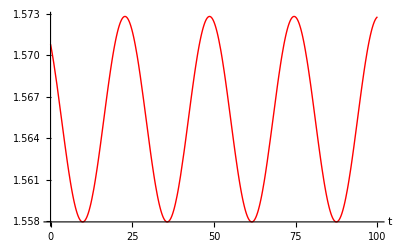

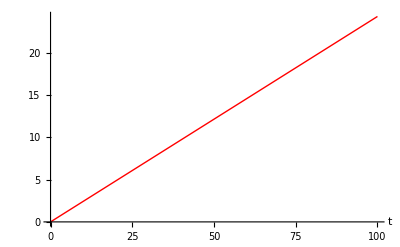

```mathematica
(*               Plot the solution curves           *)
convertList={th0->Pi/2,ps0->0,wx->-1.31816782*^-03,wy->-1.23482706*^-03,wz->-7.57091305*^-01};
Plot[{U[1,useOrder]/.convertList},{z,0,100},AxesLabel->{"t",""},PlotStyle->{{Thin,Red},{Dashed,Blue}}]
Plot[{U[2,useOrder]/.convertList},{z,0,100},AxesLabel->{"t",""},PlotStyle->{{Thin,Red},{Dashed,Blue}}]
```

archive, Insert the BVPH code, Active microswimmer in bulk fluid

```mathematica
ClearAll["Global`*"];
<<"BVPh2_0.m"
```

Package BVPh.m was successfully loaded from C:\Program Files\Wolfram Research\Mathematica\11.3\AddOns\Applications\BVPh2_0.m !

Last updated by Yin-long Zhao, 00:22, Apr. 26, 2013.

```mathematica
(*wx=-1.31816782*^-03;
wy=-1.23482706*^-03;
wz=-7.57091305*^-01;
wz1=wz+1;*)
TypeEQ = 1;
TypeL = 2;
ApproxQ = 0;
HYBRID = 0; 
TypeBase = 1;
Ntruncated = 30;
FLOAT = 1;
c0[1] = -1;
c0[2] = -1;
th0 = 0.5*Pi;

NumEQ = 2;
f[1, z_, {th_, ps_}, Lambda_] := D[th, {z, 1}] - Sin[ps]*wx - Cos[ps]*wy;f[2, z_, {th_, ps_}, Lambda_] := D[ps, {z, 1}] - Cot[th]*Cos[ps]*wx + Cot[th]*Sin[ps]*wy - wz1;

NumBC = 2;
BC[1, z_, {th_, ps_}] := (th - th0)/. z -> 0;
BC[2, z_, {th_, ps_}] := ps/. z -> 0;
zL[1] = 0;
zR[1] = 100;
zL[2] = 0;
zR[2] = 100;
U[1, 0] = th0;
U[2, 0] = wz1*z;
L[1, u_] := D[u, {z, 1}];
L[2, u_] := D[u, {z, 1}];
(*PrintInput[{th[z],ps[z]}];*)
```

```mathematica
ClearAll[time, k, uSpecial, i, tmp, c]
begin = 1;
end = 1;
Clear[lambda];  
GetInfo[];
For[k=begin,k≤end,k++,
If[PRN≥0,Print["    k = ",k]];(*2012.12.18*)
Getdelta[k-1];
GetRHS[k-1];
GetuSpecial[k];
Getu[k];
GetConstants[k];

For[i=1,i≤NumEQ,i++,
u[i,k]=u[i,k]//ExpSimplify;(*Simplify the exponent part 2013.03.28*)
If[FLOAT==1,
u[i,k]=u[i,k]//GetDigit
];
U[i,k]=Expand[U[i,k-1]+u[i,k]];
If[FLOAT==1,
U[i,k]=U[i,k]//GetDigit
];
Uz[i,k]=D[U[i,k],z];
];

(*If[IntegerQ[k/NgetErr]&&PRN≥1,GetErr[k];
If[NumberQ[ErrTotal[k]],(*c should be protected*)Print["    Err[",k,"]= ",Err[k]//N];
If[ErrTotal[k]<ErrReq,
Print["Congratulation: the required squared residual is satisfied ! "];
Return[]
];
];
];*)
];

EQ
c[2, 1, 1]
```

k = 1

{(0. wx)/wz1==0,(0. wy)/wz1==0}

-(6.12323399573676603586882014729198302312846062338790031898128063403419218957424163818359375×10^-17 wy)/wz1

```mathematica
u[1,1]//GetDigit
```

(1. wx)/wz1-(1. wx Cos[wz1 z])/wz1+(wy Sin[wz1 z])/wz1

-Graphics-

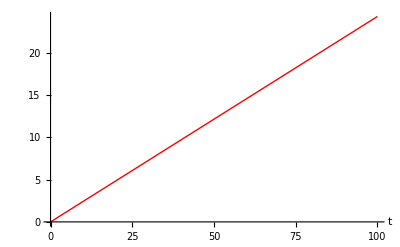

```mathematica
(*               Plot the solution curves           *)
Plot[{U[1,useOrder]},{z,0,100},AxesLabel->{"t",""},PlotStyle->{{Thin,Red},{Dashed,Blue}}]
Plot[{U[2,useOrder]},{z,0,100},AxesLabel->{"t",""},PlotStyle->{{Thin,Red},{Dashed,Blue}}]
```

Passive swimmer in shear flow

## get component w_{pi}^{klj} as function of (A_{klj} (in paper is \Omega_{klj}), k, l, j, \theta, \phi, \psi)

```mathematica
Clear["Global`*"]
$Assumptions = Aikljre[1]∈Reals&&Aikljim[1]∈Reals&&Aikljre[2]∈Reals&&Aikljim[2]∈Reals&&Aikljre[3]∈Reals&&Aikljim[3]∈Reals&&theta∈Reals&&phi∈Reals&&psi∈Reals&&k∈Integers&&l∈Integers&&j∈Integers&&i∈Integers&&nth∈Integers&&nph∈Integers&&nps∈Integers;
Aiklj[i_]=Aikljre[i]+Aikljim[i]*ⅈ;
ifft1[i_] = Aiklj[i]*ExpToTrig[Exp[2*Pi*ⅈ*(theta*k/Pi+phi*l/(2*Pi)+psi*j/(2*Pi))]]/(nth*nph*nps);
ifft2[i_] =Conjugate[Aiklj[i]]*ExpToTrig[Exp[2*Pi*ⅈ*((Pi-theta)*k/Pi+(2*Pi-phi)*l/(2*Pi)+(2*Pi-psi)*j/(2*Pi))]]/(nth*nph*nps);
wpiklj[i_,k_,l_,j_, theta_, phi_, psi_] = ExpToTrig[FullSimplify[ifft1[i]+ifft2[i]]];
FullSimplify[wpiklj[1,k,l,j,theta, phi, psi]]
FullSimplify[wpiklj[2,k,l,j,theta, phi, psi]]
FullSimplify[wpiklj[3,k,l,j,theta, phi, psi]]
```

(2 (Aikljre[1] Cos[l phi+j psi+2 k theta]-Aikljim[1] Sin[l phi+j psi+2 k theta]))/(nph nps nth)

(2 (Aikljre[2] Cos[l phi+j psi+2 k theta]-Aikljim[2] Sin[l phi+j psi+2 k theta]))/(nph nps nth)

(2 (Aikljre[3] Cos[l phi+j psi+2 k theta]-Aikljim[3] Sin[l phi+j psi+2 k theta]))/(nph nps nth)

## get component w_{pi} as function of (\theta, \phi, \psi)

```mathematica
ClearAll["Global`*"];
$Assumptions = theta∈Reals&&phi∈Reals&&psi∈Reals&&k∈Integers&&l∈Integers&&j∈Integers&&i∈Integers&&nth∈Integers&&nph∈Integers&&nps∈Integers&&nthUse∈Integers&&nphUse∈Integers&&npsUse∈Integers;
<<"BVPh2_0.m"
```

Package BVPh.m was successfully loaded from C:\Program Files\Wolfram Research\Mathematica\11.3\AddOns\Applications\BVPh2_0.m !

Last updated by Yin-long Zhao, 00:22, Apr. 26, 2013.

```mathematica
t1=Import["D:\\ecoC01B05_tau1_wm0_b_w1_fft.mat"][[1]];
A1kljre = Re[t1];
A1kljim = Im[t1];
t2=Import["D:\\ecoC01B05_tau1_wm0_b_w2_fft.mat"][[1]];
A2kljre = Re[t2];
A2kljim = Im[t2];
t3=Import["D:\\ecoC01B05_tau1_wm0_b_w3_fft.mat"][[1]];
A3kljre = Re[t3];
A3kljim = Im[t3];
Aikljre[1,k_,l_,j_] := A1kljre[[k+1,l+1,j+1]];
Aikljim[1,k_,l_,j_] := A1kljim[[k+1,l+1,j+1]];
Aikljre[2,k_,l_,j_] := A2kljre[[k+1,l+1,j+1]];
Aikljim[2,k_,l_,j_] := A2kljim[[k+1,l+1,j+1]];
Aikljre[3,k_,l_,j_] := A3kljre[[k+1,l+1,j+1]];
Aikljim[3,k_,l_,j_] := A3kljim[[k+1,l+1,j+1]];
idx1use=Import["D:\\ecoC01B05_tau1_wm0_b_w1_fft_idx.mat"][[1]];
idx2use=Import["D:\\ecoC01B05_tau1_wm0_b_w2_fft_idx.mat"][[1]];idx3use=Import["D:\\ecoC01B05_tau1_wm0_b_w3_fft_idx.mat"][[1]];
idxiuse[1,i0_]:=idx1use[[i0]];
idxiuse[2,i0_]:=idx2use[[i0]];
idxiuse[3,i0_]:=idx3use[[i0]];
nth = Dimensions[A3kljim][[1]];
nph = Dimensions[A3kljim][[2]];
nps = Dimensions[A3kljim][[3]];
```

```mathematica
numUseIdx=2;

wpiklj[i_,k_,l_,j_, theta_, phi_, psi_] = FullSimplify[(2 (Aikljre[i,k,l,j] Cos[l phi+j psi+2 k theta]-Aikljim[i,k,l,j] Sin[l phi+j psi+2 k theta]))/(nph nps nth)];
wpiklj[i,k,l,j, theta, phi, psi];
wpi[i_,theta_, phi_, psi_]:=Sum[wpiklj[i,idxiuse[i,tidx][[1]],idxiuse[i,tidx][[2]],idxiuse[i,tidx][[3]], theta, phi, psi],{tidx, 1, numUseIdx}]+wpiklj[i, 0, 0, 0, theta, phi, psi] / 2;
wpi[1,theta, phi, psi];
wpi[1,0.5*Pi, 0.25*Pi, 0]
wpi[2,0,0,0]
wpi[3,0.25*Pi, 0.5*Pi, 0.5*Pi]
```

0.193568

0.859281

-0.239645

```mathematica
pw=PageWidth/.Options[$Output];
SetOptions[$Output,PageWidth->Infinity];
wpi[1,theta, phi, psi] // InputForm
SetOptions[$Output,PageWidth->pw];
```

-0.0001866096570410253 + (-1.7029153048081684*^-6*Cos[62*phi] - 1960.88611819068*Sin[62*phi])/16384 + (-4.588689623494809*^-6*Cos[2*phi + 62*theta] - 1213.5905914763723*Sin[2*phi + 62*theta])/16384

```mathematica
TypeEQ = 1;
TypeL = 2;
ApproxQ = 0;
HYBRID = 0; 
TypeBase = 1;
Ntruncated = 30;
FLOAT = 0;
(*th0 = Pi/2;*)
(*ps0=0;*)

NumEQ = 3;
f[1, z_, {th_, ph_, ps_}, Lambda_] := D[th, {z, 1}] - (-Sin[ph] * wpi[1,th,ph,ps]+Cos[ph] * wpi[2,th,ph,ps]);
f[2, z_, {th_, ph_, ps_}, Lambda_] := D[ph, {z, 1}] - (-Cot[th] (Cos[ph] * wpi[1,th,ph,ps]+Sin[ph] * wpi[2,th,ph,ps]) + wpi[3,th,ph,ps]);f[3, z_, {th_, ph_, ps_}, Lambda_] := D[ps, {z, 1}] - (Csc[th] (Cos[ph] * wpi[1,th,ph,ps]+Sin[ph] * wpi[2,th,ph,ps]));

NumBC = 3;
BC[1, z_, {th_, ph_, ps_}] := (th - th0)/. z -> 0;
BC[2, z_, {th_, ph_, ps_}] := (ph - ph0)/. z -> 0;
BC[3, z_, {th_, ph_, ps_}] := (ps - ps0)/. z -> 0;
zL[1] = 0;
zR[1] = 10;
zL[2] = 0;
zR[2] = 10;
zL[3] = 0;
zR[3] = 10;

U[1, 0] = th0; 
U[2, 0] = ph0; 
U[3, 0] = ps0; 
L[1, u_] := D[u, {z, 1}];
L[2, u_] := D[u, {z, 1}];
L[3, u_] := D[u, {z, 1}];
c0[1] = c01;
c0[2] = c02;
c0[3] = c03;
PrintInput[{th[z],ph[z],ps[z]}]
```

The values of control parameters in BVPh:

Ntruncated  =  30

NtermMax    =  90

Nintegral   =  50

ErrReq      =  1.×10^-20

NgetErr     =  2

ComplexQ    =  0

PRN         =  1

ApproxQ     =  0

TypeL       =  2

TypeBase    =  1

HYBRID      =  0

FLOAT       =  0

Naccu       =  100

About the system of ODEs:

It has 3 differential equation(s) subject to 3 boundary conditions.

(1) Governing equation(s):

1th ODE: -Cos[ph[z]] (0.61972+(-1962.09 Cos[62 ph[z]]+1.70753×10^-6 Sin[62 ph[z]])/16384+(5887.07 Cos[62 th[z]]-0.0000265153 Sin[62 th[z]])/16384)+Sin[ph[z]] (-0.00018661+(-1.70292×10^-6 Cos[62 ph[z]]-1960.89 Sin[62 ph[z]])/16384+(-4.58869×10^-6 Cos[2 ph[z]+62 th[z]]-1213.59 Sin[2 ph[z]+62 th[z]])/16384)+th'[z] = 0,

2th ODE: -1.90745×10^-16+(-2099.12 Cos[ph[z]+2 th[z]]-5.59812×10^-6 Sin[ph[z]+2 th[z]])/16384+(1827.22 Cos[ph[z]+62 th[z]]-3.58844×10^-6 Sin[ph[z]+62 th[z]])/16384+Cot[th[z]] (Sin[ph[z]] (0.61972+(-1962.09 Cos[62 ph[z]]+1.70753×10^-6 Sin[62 ph[z]])/16384+(5887.07 Cos[62 th[z]]-0.0000265153 Sin[62 th[z]])/16384)+Cos[ph[z]] (-0.00018661+(-1.70292×10^-6 Cos[62 ph[z]]-1960.89 Sin[62 ph[z]])/16384+(-4.58869×10^-6 Cos[2 ph[z]+62 th[z]]-1213.59 Sin[2 ph[z]+62 th[z]])/16384))+ph'[z] = 0,

3th ODE: -Csc[th[z]] (Sin[ph[z]] (0.61972+(-1962.09 Cos[62 ph[z]]+1.70753×10^-6 Sin[62 ph[z]])/16384+(5887.07 Cos[62 th[z]]-0.0000265153 Sin[62 th[z]])/16384)+Cos[ph[z]] (-0.00018661+(-1.70292×10^-6 Cos[62 ph[z]]-1960.89 Sin[62 ph[z]])/16384+(-4.58869×10^-6 Cos[2 ph[z]+62 th[z]]-1213.59 Sin[2 ph[z]+62 th[z]])/16384))+ps'[z] = 0,

(2) Boundary conditions:

1th BC: -th0+th[0] = 0,

2th BC: -ph0+ph[0] = 0,

3th BC: -ps0+ps[0] = 0,

(3) Domain of the ODE:

1th ODE: 0 <= z <= 10

2th ODE: 0 <= z <= 10

3th ODE: 0 <= z <= 10

(4) Integral interval of the error:

1th ODE: 0 <= z <= 10

2th ODE: 0 <= z <= 10

3th ODE: 0 <= z <= 10

Convergence-control parameters in HAM:

(1) Initial guess(es):

u[1, 0] = th0

u[2, 0] = ph0

u[3, 0] = ps0

(2) Auxiliary linear operator(s):

L[1, u] = u'[z]

L[2, u] = u'[z]

L[3, u] = u'[z]

(3) Auxiliary function(s):

H[1, z] = 1

H[2, z] = 1

H[3, z] = 1

(4) Convergence-control parameter(s):

c0[1] = c01

c0[2] = c02

c0[3] = c03

```mathematica
useOrder = 13;
BVPh[1, useOrder];
```

Computing higher order approximations...

ApproxQ    = 0

TypeL      = 2

k = 1

Used CPU time = 0.178559 (seconds)

k = 2

Used CPU time = 19659.5 (seconds)

k = 3

Used CPU time = 20727.8 (seconds)

k = 4

```mathematica
U[1,1]
```

U[1,1]

```mathematica
pw=PageWidth/.Options[$Output];
SetOptions[$Output,PageWidth->Infinity];
InputForm[U[1,useOrder]]
SetOptions[$Output,PageWidth->pw];
(*D[U[1,useOrder],z]*)
(*U[2,useOrder] // InputForm*)
(*D[U[2,useOrder],z]*)
```

th0 - 0.6197200974539849*c01*z*Cos[ph0] + 0.000036887909511729156*c01*z*Cos[61*ph0] + 0.11971987852173585*c01*z*Cos[63*ph0] - 0.1796590181579482*c01*z*Cos[ph0 - 62*th0] - 0.21669486384509337*c01*z*Cos[ph0 + 62*th0] + 0.03703584568714515*c01*z*Cos[3*ph0 + 62*th0] - 0.0001866096570410253*c01*z*Sin[ph0] - 1.4077184803886813*^-13*c01*z*Sin[61*ph0] - 1.0407847355752181*^-10*c01*z*Sin[63*ph0] - 8.091841433022218*^-10*c01*z*Sin[ph0 - 62*th0] + 9.492198373786016*^-10*c01*z*Sin[ph0 + 62*th0] - 1.4003569407637966*^-10*c01*z*Sin[3*ph0 + 62*th0]

## calculate wx, wy, and wz using base flow method.

### strain rate Eij

```mathematica
Clear["Global`*"]
$Assumptions=_∈Reals&&z∈Reals; 
<<"BVPh2_0.m"
getRotMatrix[pn_,theta_]=Module[{tM,tn,a,b,c},
tn=Norm[pn];
a=pn.{1,0,0}/tn;
b=pn.{0,1,0}/tn;
c=pn.{0,0,1}/tn;
tM={{a^2+(1-a^2)*Cos[theta],a*b*(1-Cos[theta])+c*Sin[theta],a*c*(1-Cos[theta])-b*Sin[theta]},{a*b*(1-Cos[theta])-c*Sin[theta],b^2+(1-b^2)*Cos[theta],b*c*(1-Cos[theta])+a*Sin[theta]},{a*c*(1-Cos[theta])+b*Sin[theta],b*c*(1-Cos[theta])-a*Sin[theta],c^2+(1-c^2)*Cos[theta]}};
Transpose[tM]
];
rotM[theta_, phi_, psi_]=FullSimplify[getRotMatrix[{0,0,1},phi].getRotMatrix[{0,1,0},theta].getRotMatrix[{0,0,1},psi]];
MatrixForm[rotM[theta, phi, psi]]

z0[theta_, phi_, psi_]=FullSimplify[(rotM[theta, phi, psi].{x1,y1,z1})[[3]]];
u1[theta_, phi_, psi_]=FullSimplify[Transpose[rotM[theta, phi, psi]].{z0[theta, phi, psi],0,0}];
MatrixForm[u1[theta, phi, psi]];
Dij[theta_, phi_, psi_]=FullSimplify[Transpose[{D[u1[theta, phi, psi],{x1,1}],
D[u1[theta, phi, psi],{y1,1}],
D[u1[theta, phi, psi],{z1,1}]}]];
MatrixForm[Dij[theta, phi, psi]];
Eij[theta_, phi_, psi_]=FullSimplify[1/2*(Dij[theta, phi, psi]+Transpose[Dij[theta, phi, psi]])];
MatrixForm[Eij[theta, phi, psi]]
Sij[theta_, phi_, psi_]=FullSimplify[1/2*(Dij[theta, phi, psi]-Transpose[Dij[theta, phi, psi]])];
MatrixForm[Sij[theta, phi, psi]]

(*wEbaseList = {{wE1x, wE1y, wE1z}, {wE2x, wE2y, wE2z}, {wE3x, wE3y, wE3z}, {wE4x, wE4y, wE4z}, {wE5x, wE5y, wE5z}};*)
(*wEbaseList = {{0, 0, wE1z}, {0, 0, wE2z}, {0, 0, 0}, {wE4x, wE4y, 0}, {-wE4y, wE4x, 0}};*)
wE4y=0.8;
wEbaseList = {{0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, wE4y, 0}, {-wE4y, 0, 0}};
(*wEbaseList = {{-6.28396028*^-03,-3.59458140*^-03,-2.61018491*^-01}, {-0.03147468,0.0263663,0.02524755}, {0.00261925,-0.01267259,0.53873059}, {-0.00136591,0.93546161,0.02544228}, {-9.80745910*^-01,-2.25191824*^-02,-4.64097001*^-03}};*)(*wEbaseList = {{0,0,-2.61018491*^-01}, {-0.03147468,0.0263663,0.02524755}, {0,-0.01267259,0.53873059}, {0,0.93546161,0.02544228}, {-9.80745910*^-01,-2.25191824*^-02,0}};*)(*wEbaseList = {{0,0,-2.61018491*^-01}, {0,0,0}, {0,0,0.53873059}, {0,0.93546161,0}, {-9.80745910*^-01,0,0}};*)
MatrixForm[wEbaseList]
```

Package BVPh.m was successfully loaded from C:\Program Files\Wolfram Research\Mathematica\11.3\AddOns\Applications\BVPh2_0.m !

Last updated by Yin-long Zhao, 00:22, Apr. 26, 2013.

(Cos[phi] Cos[psi] Cos[theta]-Sin[phi] Sin[psi] | -Cos[psi] Sin[phi]-Cos[phi] Cos[theta] Sin[psi] | Cos[phi] Sin[theta]
Cos[psi] Cos[theta] Sin[phi]+Cos[phi] Sin[psi] | Cos[phi] Cos[psi]-Cos[theta] Sin[phi] Sin[psi] | Sin[phi] Sin[theta]
-Cos[psi] Sin[theta] | Sin[psi] Sin[theta] | Cos[theta])

(Cos[psi] (-Cos[phi] Cos[psi] Cos[theta]+Sin[phi] Sin[psi]) Sin[theta] | 1/4 (2 Cos[2 psi] Sin[phi] Sin[theta]+Cos[phi] Sin[2 psi] Sin[2 theta]) | 1/2 (Cos[phi] Cos[psi] Cos[2 theta]-Cos[theta] Sin[phi] Sin[psi])
1/4 (2 Cos[2 psi] Sin[phi] Sin[theta]+Cos[phi] Sin[2 psi] Sin[2 theta]) | -Sin[psi] (Cos[psi] Sin[phi]+Cos[phi] Cos[theta] Sin[psi]) Sin[theta] | 1/2 (-Cos[psi] Cos[theta] Sin[phi]-Cos[phi] Cos[2 theta] Sin[psi])
1/2 (Cos[phi] Cos[psi] Cos[2 theta]-Cos[theta] Sin[phi] Sin[psi]) | 1/2 (-Cos[psi] Cos[theta] Sin[phi]-Cos[phi] Cos[2 theta] Sin[psi]) | Cos[phi] Cos[theta] Sin[theta])

(0 | -1/2 Sin[phi] Sin[theta] | 1/2 (Cos[phi] Cos[psi]-Cos[theta] Sin[phi] Sin[psi])
1/2 Sin[phi] Sin[theta] | 0 | 1/2 (-Cos[psi] Cos[theta] Sin[phi]-Cos[phi] Sin[psi])
1/2 (-Cos[phi] Cos[psi]+Cos[theta] Sin[phi] Sin[psi]) | 1/2 (Cos[psi] Cos[theta] Sin[phi]+Cos[phi] Sin[psi]) | 0)

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0.8 | 0
-0.8 | 0 | 0)

```mathematica
EbaseFct[theta_, phi_, psi_]:={Eij[theta, phi, psi][[1, 1]], 
Eij[theta, phi, psi][[3, 3]], 
Eij[theta, phi, psi][[1, 2]], 
Eij[theta, phi, psi][[1, 3]], 
Eij[theta, phi, psi][[2, 3]]}
wELoc[theta_, phi_, psi_] = FullSimplify[Total[EbaseFct[theta, phi, psi]*wEbaseList]];
MatrixForm[wELoc[theta, phi, psi]] ;
wE[theta_, phi_, psi_]=FullSimplify[rotM[theta, phi, psi].wELoc[theta, phi, psi]]; 
(*wE[theta_, phi_, psi_]=FullSimplify[{(Cos[phi] Cos[psi] Cos[theta]-Sin[phi] Sin[psi]) (0.490372955 Cos[psi] Cos[theta] Sin[phi]+Cos[phi] (0.490372955 Cos[2 theta] Sin[psi]-0.03147468 Cos[theta] Sin[theta]))+(-Cos[psi] Sin[phi]-Cos[phi] Cos[theta] Sin[psi]) (Sin[phi] (0.0112595912 Cos[psi] Cos[theta]-0.467730805 Cos[theta] Sin[psi])+Cos[phi] (Cos[2 theta] (0.46773080499999997 Cos[psi]+0.0112595912 Sin[psi])+Cos[theta] (0.026366300000000002-0.01267259 Cos[psi] Sin[psi]) Sin[theta]))+Cos[phi] Sin[theta] (Sin[phi] (-0.01272114 Cos[theta] Sin[psi]+(0.269365295 Cos[2 psi]-0.261018491 Cos[psi] Sin[psi]) Sin[theta])+Cos[phi] (0.01272114 Cos[psi] Cos[2 theta]+Cos[theta] (0.02524755+0.261018491 Cos[psi]^2+0.53873059 Cos[psi] Sin[psi]) Sin[theta])),(Cos[psi] Cos[theta] Sin[phi]+Cos[phi] Sin[psi]) (0.490372955 Cos[psi] Cos[theta] Sin[phi]+Cos[phi] (0.490372955 Cos[2 theta] Sin[psi]-0.03147468 Cos[theta] Sin[theta]))+(Cos[phi] Cos[psi]-Cos[theta] Sin[phi] Sin[psi]) (Sin[phi] (0.0112595912 Cos[psi] Cos[theta]-0.467730805 Cos[theta] Sin[psi])+Cos[phi] (Cos[2 theta] (0.46773080499999997 Cos[psi]+0.0112595912 Sin[psi])+Cos[theta] (0.026366300000000002-0.01267259 Cos[psi] Sin[psi]) Sin[theta]))+Sin[phi] Sin[theta] (Sin[phi] (-0.01272114 Cos[theta] Sin[psi]+(0.269365295 Cos[2 psi]-0.261018491 Cos[psi] Sin[psi]) Sin[theta])+Cos[phi] (0.01272114 Cos[psi] Cos[2 theta]+Cos[theta] (0.02524755+0.261018491 Cos[psi]^2+0.53873059 Cos[psi] Sin[psi]) Sin[theta])),Sin[phi] (-0.01272114 Cos[theta]^2 Sin[psi]+Cos[theta] (-0.47905188+0.25804422000000005 Cos[2 psi]-0.2497588998 Cos[psi] Sin[psi]) Sin[theta])+Cos[phi] (0.01272114 Cos[psi] Cos[theta]^3+(0.0112595912 Cos[2 theta] Sin[psi]^2+Cos[theta]^2 (0.02524755+0.261018491 Cos[psi]^2+0.51608844 Cos[psi] Sin[psi])) Sin[theta]+Cos[theta] (0.015585392499999998 Cos[psi]+0.026366300000000002 Sin[psi]) Sin[theta]^2+0.022642150000000028 Cos[psi] Sin[psi] Sin[theta]^3)}];*)
```

```mathematica
pw=PageWidth/.Options[$Output];
SetOptions[$Output,PageWidth->Infinity];
FortranForm[wE[theta, phi, psi]]
(*wE[theta, phi, psi]*)
SetOptions[$Output,PageWidth->pw];
```

List(Cos(phi)*(0.20000000000000007 - 0.2*Cos(2*theta))*Sin(phi),0.1 - 0.1*Cos(2*phi) + 0.05*Cos(2*phi - 2*theta) + 0.30000000000000004*Cos(2*theta) + 0.05*Cos(2*(phi + theta)),-0.4*Cos(theta)*Sin(phi)*Sin(theta))

```mathematica
wE[theta, phi, psi][[1]] 
wE[theta, phi, psi][[2]] 
wE[theta, phi, psi][[3]]
```

Cos[phi] (0.2-0.2 Cos[2 theta]) Sin[phi]

0.1-0.1 Cos[2 phi]+0.05 Cos[2 phi-2 theta]+0.3 Cos[2 theta]+0.05 Cos[2 (phi+theta)]

-0.4 Cos[theta] Sin[phi] Sin[theta]

```mathematica
wS = {0, 0.5, 0} ; (*simple shear flow*)
w[theta_, phi_, psi_]=wE[theta, phi, psi]+wS;
wpi[1,theta_, phi_, psi_] = FullSimplify[w[theta, phi, psi][[1]]]
wpi[2,theta_, phi_, psi_] = FullSimplify[w[theta, phi, psi][[2]]]
wpi[3,theta_, phi_, psi_] = FullSimplify[w[theta, phi, psi][[3]]]
```

Cos[phi] (0.2-0.2 Cos[2 theta]) Sin[phi]

0.6-0.1 Cos[2 phi]+0.05 Cos[2 phi-2 theta]+0.3 Cos[2 theta]+0.05 Cos[2 (phi+theta)]

-0.4 Cos[theta] Sin[phi] Sin[theta]

```mathematica
TypeEQ = 1;
TypeL = 2;
ApproxQ = 0;
HYBRID = 0; 
TypeBase = 1;
Ntruncated = 30;
FLOAT = 0;
(*th0 = Pi/2;*)
(*ps0=0;*)

NumEQ = 3;
f[1, z_, {th_, ph_, ps_}, Lambda_] := D[th, {z, 1}] - FullSimplify[(-Sin[ph] * wpi[1,th,ph,ps]+Cos[ph] * wpi[2,th,ph,ps])];
f[2, z_, {th_, ph_, ps_}, Lambda_] := D[ph, {z, 1}] - FullSimplify[(-Cot[th] (Cos[ph] * wpi[1,th,ph,ps]+Sin[ph] * wpi[2,th,ph,ps]) + wpi[3,th,ph,ps])];f[3, z_, {th_, ph_, ps_}, Lambda_] := D[ps, {z, 1}] - FullSimplify[(Csc[th] (Cos[ph] * wpi[1,th,ph,ps]+Sin[ph] * wpi[2,th,ph,ps]))];

NumBC = 3;
BC[1, z_, {th_, ph_, ps_}] := (th - th0)/. z -> 0;
BC[2, z_, {th_, ph_, ps_}] := (ph - ph0)/. z -> 0;
BC[3, z_, {th_, ph_, ps_}] := (ps - ps0)/. z -> 0;
zL[1] = 0;
zR[1] = 10;
zL[2] = 0;
zR[2] = 10;
zL[3] = 0;
zR[3] = 10;

U[1, 0] = th0; 
U[2, 0] = ph0; 
U[3, 0] = ps0; 
L[1, u_] := D[u, {z, 1}];
L[2, u_] := D[u, {z, 1}];
L[3, u_] := D[u, {z, 1}];
myc0=-0.5;
c01=myc0;
c02=myc0;
c03=myc0;
c0[1] = c01;
c0[2] = c02;
c0[3] = c03;
PrintInput[{th[z],ph[z],ps[z]}]
```

The values of control parameters in BVPh:

Ntruncated  =  30

NtermMax    =  90

Nintegral   =  50

ErrReq      =  1.×10^-20

NgetErr     =  2

ComplexQ    =  0

PRN         =  1

ApproxQ     =  0

TypeL       =  2

TypeBase    =  1

HYBRID      =  0

FLOAT       =  0

Naccu       =  100

About the system of ODEs:

It has 3 differential equation(s) subject to 3 boundary conditions.

(1) Governing equation(s):

1th ODE: -Cos[ph[z]] (0.5+0.4 Cos[2 th[z]])+th'[z] = 0,

2th ODE: -(-0.9 Cot[th[z]]-1.38778×10^-17 Cos[3 th[z]] Csc[th[z]]) Sin[ph[z]]+ph'[z] = 0,

3th ODE: -(0.7+0.2 Cos[2 th[z]]) Csc[th[z]] Sin[ph[z]]+ps'[z] = 0,

(2) Boundary conditions:

1th BC: -th0+th[0] = 0,

2th BC: -ph0+ph[0] = 0,

3th BC: -ps0+ps[0] = 0,

(3) Domain of the ODE:

1th ODE: 0 <= z <= 10

2th ODE: 0 <= z <= 10

3th ODE: 0 <= z <= 10

(4) Integral interval of the error:

1th ODE: 0 <= z <= 10

2th ODE: 0 <= z <= 10

3th ODE: 0 <= z <= 10

Convergence-control parameters in HAM:

(1) Initial guess(es):

u[1, 0] = th0

u[2, 0] = ph0

u[3, 0] = ps0

(2) Auxiliary linear operator(s):

L[1, u] = u'[z]

L[2, u] = u'[z]

L[3, u] = u'[z]

(3) Auxiliary function(s):

H[1, z] = 1

H[2, z] = 1

H[3, z] = 1

(4) Convergence-control parameter(s):

c0[1] = -0.5

c0[2] = -0.5

c0[3] = -0.5

```mathematica
useOrder = 2;
BVPh[1, useOrder];
```

Computing higher order approximations...

ApproxQ    = 0

TypeL      = 2

k = 1

Used CPU time = 5.99401 (seconds)

k = 2

```mathematica
BVPh[useOrder+1, useOrder*2];
```

Computing higher order approximations...

ApproxQ    = 0

TypeL      = 2

k = 3

Used CPU time = 28.8116 (seconds)

k = 4

```mathematica
U[1,useOrder]
```

U[1,useOrder]

```mathematica
convertList={th0->0.1,ph0->0.1, ps0->0.1,c0->0.5}
Re[U[1,useOrder]/.convertList]
```

{th0→0.1,ph0→0.1,ps0→0.1,c0→0.5}

0.1+Re[0.665678 z-(0.00757667+0. ⅈ) z^2]

```mathematica
convertList
Re[U[1,useOrder]/.convertList]
```

{th0→0.1,ph0→0.1,ps0→0.1,c0→0.5}

0.1+Re[0.665678 z-(0.00757667+0. ⅈ) z^2]

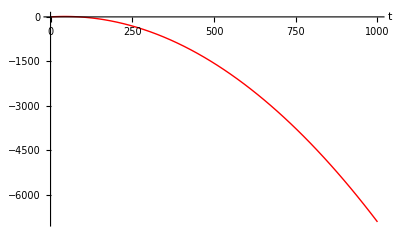

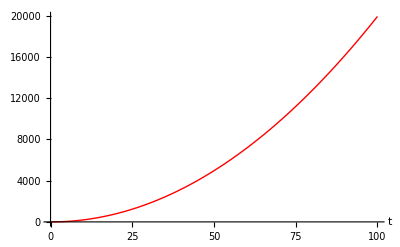

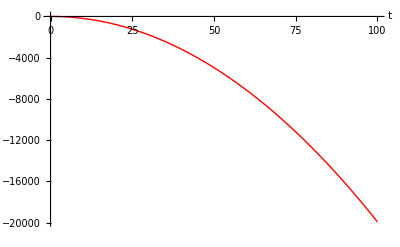

```mathematica
(*               Plot the solution curves           *)
convertList={th0->0.1,ph0->0.1, ps0->0.1,c0->-0.5};
Plot[{Re[U[1,useOrder]/.convertList]},{z,0,1000},AxesLabel->{"t",""},PlotStyle->{{Thin,Red},{Dashed,Blue}}]
Plot[{Re[U[2,useOrder]/.convertList]},{z,0,100},AxesLabel->{"t",""},PlotStyle->{{Thin,Red},{Dashed,Blue}}]
Plot[{Re[U[3,useOrder]/.convertList]},{z,0,100},AxesLabel->{"t",""},PlotStyle->{{Thin,Red},{Dashed,Blue}}]
```

archived

```mathematica
1/2 ((Cos[ϕ] Cos[ψ] Cos[θ]-Sin[ϕ] Sin[ψ]) (Cos[ϕ] Cos[2 θ] (wE4x Cos[ψ]-wE5x Sin[ψ])+Sin[ϕ] (-Cos[θ] (wE5x Cos[ψ]+wE4x Sin[ψ])+(wE3x Cos[2 ψ]+wE1x Sin[2 ψ]) Sin[θ])-1/2 Cos[ϕ] (wE1x-2 wE2x+wE1x Cos[2 ψ]-wE3x Sin[2 ψ]) Sin[2 θ])+Cos[ϕ] Sin[θ] (Cos[ϕ] Cos[2 θ] (wE4z Cos[ψ]-wE5z Sin[ψ])+Sin[ϕ] (-Cos[θ] (wE5z Cos[ψ]+wE4z Sin[ψ])+(wE3z Cos[2 ψ]+wE1z Sin[2 ψ]) Sin[θ])-1/2 Cos[ϕ] (wE1z-2 wE2z+wE1z Cos[2 ψ]-wE3z Sin[2 ψ]) Sin[2 θ])+1/2 (Cos[ψ] Sin[ϕ]+Cos[ϕ] Cos[θ] Sin[ψ]) (2 Sin[ϕ] (wE5y Cos[ψ] Cos[θ]+wE4y Cos[θ] Sin[ψ]-(wE3y Cos[2 ψ]+wE1y Sin[2 ψ]) Sin[θ])+Cos[ϕ] (2 Cos[2 θ] (-wE4y Cos[ψ]+wE5y Sin[ψ])+(wE1y-2 wE2y+wE1y Cos[2 ψ]-wE3y Sin[2 ψ]) Sin[2 θ])))
```

1/2 ((Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ]) (Cos[2 θ] Cos[ϕ] (wE4x Cos[ψ]-wE5x Sin[ψ])-1/2 Cos[ϕ] Sin[2 θ] (wE1x-2 wE2x+wE1x Cos[2 ψ]-wE3x Sin[2 ψ])+Sin[ϕ] (-Cos[θ] (wE5x Cos[ψ]+wE4x Sin[ψ])+Sin[θ] (wE3x Cos[2 ψ]+wE1x Sin[2 ψ])))+Cos[ϕ] Sin[θ] (Cos[2 θ] Cos[ϕ] (wE4z Cos[ψ]-wE5z Sin[ψ])-1/2 Cos[ϕ] Sin[2 θ] (wE1z-2 wE2z+wE1z Cos[2 ψ]-wE3z Sin[2 ψ])+Sin[ϕ] (-Cos[θ] (wE5z Cos[ψ]+wE4z Sin[ψ])+Sin[θ] (wE3z Cos[2 ψ]+wE1z Sin[2 ψ])))+1/2 (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ]) (2 Sin[ϕ] (wE5y Cos[θ] Cos[ψ]+wE4y Cos[θ] Sin[ψ]-Sin[θ] (wE3y Cos[2 ψ]+wE1y Sin[2 ψ]))+Cos[ϕ] (2 Cos[2 θ] (-wE4y Cos[ψ]+wE5y Sin[ψ])+Sin[2 θ] (wE1y-2 wE2y+wE1y Cos[2 ψ]-wE3y Sin[2 ψ]))))

```mathematica
1/2 ((Cos[ψ] Cos[θ] Sin[ϕ]+Cos[ϕ] Sin[ψ]) (Cos[ϕ] Cos[2 θ] (wE4x Cos[ψ]-wE5x Sin[ψ])+Sin[ϕ] (-Cos[θ] (wE5x Cos[ψ]+wE4x Sin[ψ])+(wE3x Cos[2 ψ]+wE1x Sin[2 ψ]) Sin[θ])-1/2 Cos[ϕ] (wE1x-2 wE2x+wE1x Cos[2 ψ]-wE3x Sin[2 ψ]) Sin[2 θ])+(Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ]) (Cos[ϕ] Cos[2 θ] (wE4y Cos[ψ]-wE5y Sin[ψ])+Sin[ϕ] (-Cos[θ] (wE5y Cos[ψ]+wE4y Sin[ψ])+(wE3y Cos[2 ψ]+wE1y Sin[2 ψ]) Sin[θ])-1/2 Cos[ϕ] (wE1y-2 wE2y+wE1y Cos[2 ψ]-wE3y Sin[2 ψ]) Sin[2 θ])+Sin[ϕ] Sin[θ] (Cos[ϕ] Cos[2 θ] (wE4z Cos[ψ]-wE5z Sin[ψ])+Sin[ϕ] (-Cos[θ] (wE5z Cos[ψ]+wE4z Sin[ψ])+(wE3z Cos[2 ψ]+wE1z Sin[2 ψ]) Sin[θ])-1/2 Cos[ϕ] (wE1z-2 wE2z+wE1z Cos[2 ψ]-wE3z Sin[2 ψ]) Sin[2 θ]))
```

1/2 ((Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ]) (Cos[2 θ] Cos[ϕ] (wE4x Cos[ψ]-wE5x Sin[ψ])-1/2 Cos[ϕ] Sin[2 θ] (wE1x-2 wE2x+wE1x Cos[2 ψ]-wE3x Sin[2 ψ])+Sin[ϕ] (-Cos[θ] (wE5x Cos[ψ]+wE4x Sin[ψ])+Sin[θ] (wE3x Cos[2 ψ]+wE1x Sin[2 ψ])))+(Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ]) (Cos[2 θ] Cos[ϕ] (wE4y Cos[ψ]-wE5y Sin[ψ])-1/2 Cos[ϕ] Sin[2 θ] (wE1y-2 wE2y+wE1y Cos[2 ψ]-wE3y Sin[2 ψ])+Sin[ϕ] (-Cos[θ] (wE5y Cos[ψ]+wE4y Sin[ψ])+Sin[θ] (wE3y Cos[2 ψ]+wE1y Sin[2 ψ])))+Sin[θ] Sin[ϕ] (Cos[2 θ] Cos[ϕ] (wE4z Cos[ψ]-wE5z Sin[ψ])-1/2 Cos[ϕ] Sin[2 θ] (wE1z-2 wE2z+wE1z Cos[2 ψ]-wE3z Sin[2 ψ])+Sin[ϕ] (-Cos[θ] (wE5z Cos[ψ]+wE4z Sin[ψ])+Sin[θ] (wE3z Cos[2 ψ]+wE1z Sin[2 ψ]))))

```mathematica
1/4 (Cos[ϕ] (wE4z Cos[ψ] Cos[θ]+wE4z Cos[ψ] Cos[3 θ]-2 wE5z Cos[θ] Cos[2 θ] Sin[ψ]-2 (Cos[2 θ] (wE4x Cos[ψ]^2-(wE4y+wE5x) Cos[ψ] Sin[ψ]+wE5y Sin[ψ]^2)+Cos[θ]^2 (wE1z-2 wE2z+wE1z Cos[2 ψ]-wE3z Sin[2 ψ])) Sin[θ]+Cos[θ] ((3 wE1x-4 wE2x+wE3y) Cos[ψ]+(wE1x-wE3y) Cos[3 ψ]-(wE1y-4 wE2y+wE3x) Sin[ψ]-(wE1y+wE3x) Sin[3 ψ]) Sin[θ]^2)+Sin[ϕ] (-2 Cos[θ]^2 (wE5z Cos[ψ]+wE4z Sin[ψ])+2 (-wE3x Cos[ψ] Cos[2 ψ]-2 wE1x Cos[ψ]^2 Sin[ψ]+Sin[ψ] (wE3y Cos[2 ψ]+wE1y Sin[2 ψ])) Sin[θ]^2+(wE5x Cos[ψ]^2+wE3z Cos[2 ψ]+(wE4x-wE5y) Cos[ψ] Sin[ψ]-wE4y Sin[ψ]^2+wE1z Sin[2 ψ]) Sin[2 θ]))
```

1/4  (Sin[ϕ] (-2 Cos[θ]^2 (wE5z Cos[ψ]+wE4z Sin[ψ])+Sin[2 θ] (wE5x Cos[ψ]^2+wE3z Cos[2 ψ]+(wE4x-wE5y) Cos[ψ] Sin[ψ]-wE4y Sin[ψ]^2+wE1z Sin[2 ψ])+2 Sin[θ]^2 (-wE3x Cos[ψ] Cos[2 ψ]-2 wE1x Cos[ψ]^2 Sin[ψ]+Sin[ψ] (wE3y Cos[2 ψ]+wE1y Sin[2 ψ])))+Cos[ϕ] (wE4z Cos[θ] Cos[ψ]+wE4z Cos[3 θ] Cos[ψ]-2 wE5z Cos[θ] Cos[2 θ] Sin[ψ]-2 Sin[θ] (Cos[2 θ] (wE4x Cos[ψ]^2-(wE4y+wE5x) Cos[ψ] Sin[ψ]+wE5y Sin[ψ]^2)+Cos[θ]^2 (wE1z-2 wE2z+wE1z Cos[2 ψ]-wE3z Sin[2 ψ]))+Cos[θ] Sin[θ]^2 ((3 wE1x-4 wE2x+wE3y) Cos[ψ]+(wE1x-wE3y) Cos[3 ψ]-(wE1y-4 wE2y+wE3x) Sin[ψ]-(wE1y+wE3x) Sin[3 ψ])))